https://en.wikipedia.org/wiki/Fabry%E2%80%93P%C3%A9rot_interferometer

```mathematica
CFinConv=Function[fin,1/(Sin[π/(2 fin)])^2];
N[coeffin[200]]
FPTrans=Function[{cfin,δ},1/(1+cfin* (Sin[δ/2])^2)];
```

coeffin[200.]

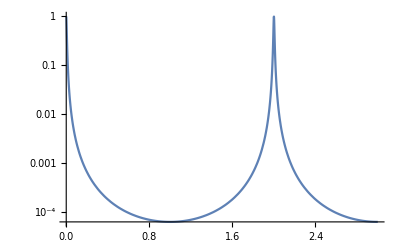

```mathematica
fineval=200;
LogPlot[FPTrans[CFinConv[fineval],x π],{x,0,3},PlotRange->All]
```

```mathematica
peakδ=1.*π/fineval;
Ppeak=NIntegrate[FPTrans[CFinConv[fineval],x],{x,-peakδ,peakδ}]
Pback=NIntegrate[FPTrans[CFinConv[fineval],x],{x,peakδ,π-peakδ}]
Pback/Ppeak
```

0.024674

0.012335

0.499921

```mathematica
PRatioWidths=Function[{fin,widths},Module[{locpeakδ},
locpeakδ=widths*π/fineval; (*max value  ~0.25/(π/fineval) *)
Ppeak=NIntegrate[FPTrans[CFinConv[fin],x],{x,-locpeakδ,locpeakδ}];
Pback=NIntegrate[FPTrans[CFinConv[fin],x],{x,locpeakδ,π-locpeakδ}];
Pback/Ppeak]]
```

Function[{fin,widths},Module[{locpeakδ},locpeakδ=(widths π)/fineval;Ppeak=NIntegrate[FPTrans[CFinConv[fin],x],{x,-locpeakδ,locpeakδ}];Pback=NIntegrate[FPTrans[CFinConv[fin],x],{x,locpeakδ,π-locpeakδ}];Pback/Ppeak]]

0.0217105

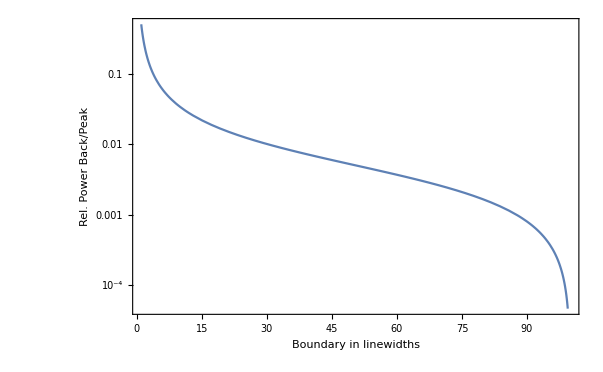

```mathematica
PRatioWidths[200,15]
LogPlot[PRatioWidths[200,x],{x,1,100},FrameLabel->{"Boundary in linewidths","Rel. Power Back/Peak"},Frame->True]
```

```mathematica
0.25/(π/200.)
```

15.9155

```mathematica
ArcTan[15.*(2π)/360]*1
```

0.256053

```mathematica
1.7/2.2
```

0.772727

```mathematica
Tan[0.03/0.7]*360/(2π)
```

2.45704